# Functions for Modelling Lift, Drag and Moment

Defining functions

```mathematica
onPositive[x_]:=(1+Sign[x])/2;
onNegative[x_]:=1-(1+Sign[x])/2;
onPositiveBetween[xmin_,xmax_,x_]:=(1+Sign[x-xmin])(1+Sign[xmax-x])/4;
f1=.6;
Sign1[x_]:=Sign[x];
a=0.4;
e=0.95;
```

```mathematica
x0=.;
xw=.;
ap=.;
an=.;
awp=.;
awn=.;
CLalpha=.;
e=.;
AR=.;
Cm0=.;
Cmfs=.;
Cd0=.;
```

```mathematica
LogisticFunc[x_]:=1/(1+N[E,6]^(- x));
```

```mathematica
CForm[1/(1+N[E,6]^(- x))]
```

1/(1 + Power(2.71828,-x))

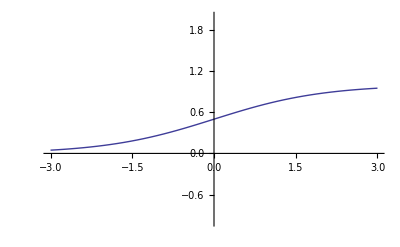

```mathematica
Plot[LogisticFunc[alpha],{alpha,-3,3},PlotRange->{-1,2}]
```

```mathematica
fw[x_,x0_,xw_]=LogisticFunc[2(x-x0)/xw];
f1=fw[alpha,ap,awp]+fw[-alpha,an,awn];
```

```mathematica
Plot[f1,{alpha,-10,10},PlotRange->{-1,2}]
```

-Graphics-

```mathematica
y1=Sin[2 alpha];
y2=Sin[alpha]^2;
CL:= CLalpha alpha(1-f1)+N[(1/Sqrt[2]),6] y1 f1;

Cdi:= (1-f1)(CLalpha alpha)^2/(N[Pi,6] e AR)+y2 f1;
```

```mathematica
Cm:= (1-f1)Cm0+Cmfs f1 Sign[alpha];
```

```mathematica
Cdi
```

(0.335063 (1-1/(1+2.71828^(-(2 (-alpha-an))/awn))-1/(1+2.71828^(-(2 (alpha-ap))/awp))) alpha^2 CLalpha^2)/AR+(1/(1+2.71828^(-(2 (-alpha-an))/awn))+1/(1+2.71828^(-(2 (alpha-ap))/awp))) Sin[alpha]^2

```mathematica
Cdi1:= (CLalpha alpha)^2/(Pi e AR);
```

```mathematica
f1
```

1/(1+2.71828^(-(2 (-alpha-an))/awn))+1/(1+2.71828^(-(2 (alpha-ap))/awp))

```mathematica
Cdi2:= y2 ;
```

```mathematica
Cd=Cd0+Cdi
```

Cd0+(0.335063 (1-1/(1+2.71828^(-(2 (-alpha-an))/awn))-1/(1+2.71828^(-(2 (alpha-ap))/awp))) alpha^2 CLalpha^2)/AR+(1/(1+2.71828^(-(2 (-alpha-an))/awn))+1/(1+2.71828^(-(2 (alpha-ap))/awp))) Sin[alpha]^2

```mathematica
CN:=Cd Sin[alpha]+CL Cos[alpha]
```

```mathematica
Cd
```

Cd0+(0.335063 (1-1/(1+2.71828^(-(2 (-alpha-an))/awn))-1/(1+2.71828^(-(2 (alpha-ap))/awp))) alpha^2 CLalpha^2)/AR+(1/(1+2.71828^(-(2 (-alpha-an))/awn))+1/(1+2.71828^(-(2 (alpha-ap))/awp))) Sin[alpha]^2

```mathematica
CL
```

(1-1/(1+2.71828^(-(2 (-alpha-an))/awn))-1/(1+2.71828^(-(2 (alpha-ap))/awp))) alpha CLalpha+0.707107 (1/(1+2.71828^(-(2 (-alpha-an))/awn))+1/(1+2.71828^(-(2 (alpha-ap))/awp))) Sin[2 alpha]

```mathematica
CN
```

Sin[alpha] (0.01+1.0722 (1-1/(1+2.71828^(-20. (-0.5-alpha)))-1/(1+2.71828^(-20. (-0.5+alpha)))) alpha^2+(1/(1+2.71828^(-20. (-0.5-alpha)))+1/(1+2.71828^(-20. (-0.5+alpha)))) Sin[alpha]^2)+Cos[alpha] (4 (1-1/(1+2.71828^(-20. (-0.5-alpha)))-1/(1+2.71828^(-20. (-0.5+alpha)))) alpha+0.707107 (1/(1+2.71828^(-20. (-0.5-alpha)))+1/(1+2.71828^(-20. (-0.5+alpha)))) Sin[2 alpha])

```mathematica
Simplify[CN]
```

Sin[alpha] (Cd0+(0.335063 (1-1/(1+2.71828^((2 (alpha+an))/awn))-1/(1+2.71828^(-(2 (alpha-ap))/awp))) alpha^2 CLalpha^2)/AR+(1/(1+2.71828^((2 (alpha+an))/awn))+1/(1+2.71828^(-(2 (alpha-ap))/awp))) Sin[alpha]^2)+Cos[alpha] ((1-1/(1+2.71828^((2 (alpha+an))/awn))-1/(1+2.71828^(-(2 (alpha-ap))/awp))) alpha CLalpha+0.707107 (1/(1+2.71828^((2 (alpha+an))/awn))+1/(1+2.71828^(-(2 (alpha-ap))/awp))) Sin[2 alpha])

```mathematica
CT:=Cd Cos[alpha]-CL Sin[alpha]
```

```mathematica
x0=.;
xw=.;
ap=.;
an=.;
awp=.;
awn=.;
CLalpha=.;
e=.;
AR=.;
Cm0=.;
Cmfs=.;
Cd0=.;
```

```mathematica
CForm[CL]
```

(1 - 1/(1 + Power(2.71828,(-2*(-alpha - an))/awn)) - 
      1/(1 + Power(2.71828,(-2*(alpha - ap))/awp)))*alpha*CLalpha + 
   0.707107*(1/(1 + Power(2.71828,(-2*(-alpha - an))/awn)) + 
      1/(1 + Power(2.71828,(-2*(alpha - ap))/awp)))*Sin(2*alpha)

```mathematica
CForm[Cdi]
```

(0.31831*(1 - 1/(1 + Power(2.71828,(-2*(-alpha - an))/awn)) - 
        1/(1 + Power(2.71828,(-2*(alpha - ap))/awp)))*Power(alpha,2)*Power(CLalpha,2))/(AR*e) + 
   (1/(1 + Power(2.71828,(-2*(-alpha - an))/awn)) + 
      1/(1 + Power(2.71828,(-2*(alpha - ap))/awp)))*Power(Sin(alpha),2)

```mathematica
CForm[Cm]
```

(1 - 1/(1 + Power(2.71828,(-2*(-alpha - an))/awn)) - 
      1/(1 + Power(2.71828,(-2*(alpha - ap))/awp)))*Cm0 + 
   (1/(1 + Power(2.71828,(-2*(-alpha - an))/awn)) + 
      1/(1 + Power(2.71828,(-2*(alpha - ap))/awp)))*Cmfs*Sign(alpha)

```mathematica
x0=.3;
xw=.1;
ap=.5;
an=.5;
awp=.1;
awn=.1;

expclp=6;
expcln=9;
CLalpha=4;
e=0.95;
AR=5;
Cm0=-.05;
Cmfs=-.1;
Cd0=0.01;
```

```mathematica
Cd
```

0.01+1.0722 (1-1/(1+2.71828^(-20. (-0.5-alpha)))-1/(1+2.71828^(-20. (-0.5+alpha)))) alpha^2+(1/(1+2.71828^(-20. (-0.5-alpha)))+1/(1+2.71828^(-20. (-0.5+alpha)))) Sin[alpha]^2

```mathematica
f1
```

1/(1+2.71828^(-20. (-0.5-alpha)))+1/(1+2.71828^(-20. (-0.5+alpha)))

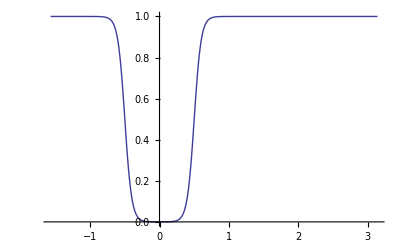

```mathematica
Plot[ {f1} ,{alpha,-Pi/2, Pi}]
```

```mathematica
CL
```

4 (1-1/(1+2.71828^(-20. (-0.5-alpha)))-1/(1+2.71828^(-20. (-0.5+alpha)))) alpha+0.707107 (1/(1+2.71828^(-20. (-0.5-alpha)))+1/(1+2.71828^(-20. (-0.5+alpha)))) Sin[2 alpha]

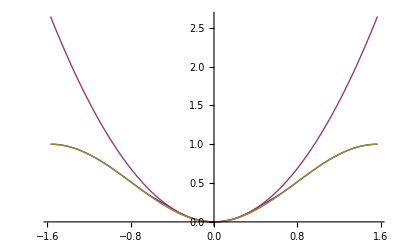

```mathematica
Plot[ {Cdi,Cdi1,Cdi2} ,{alpha,-Pi/2, Pi/2}]
```

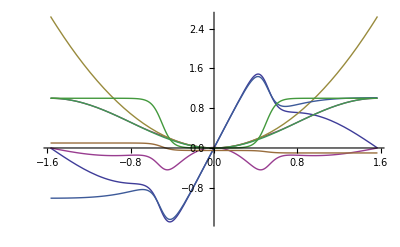

```mathematica
Plot[ {CL,Cdi,Cdi1,Cdi2,CN,CT,Cm,f1} ,{alpha,-Pi/2, Pi/2}]
```

```mathematica
CN
```

Sin[alpha] (0.01+1.0722 (1-1/(1+2.71828^(-20. (-0.5-alpha)))-1/(1+2.71828^(-20. (-0.5+alpha)))) alpha^2+(1/(1+2.71828^(-20. (-0.5-alpha)))+1/(1+2.71828^(-20. (-0.5+alpha)))) Sin[alpha]^2)+Cos[alpha] (4 (1-1/(1+2.71828^(-20. (-0.5-alpha)))-1/(1+2.71828^(-20. (-0.5+alpha)))) alpha+0.707107 (1/(1+2.71828^(-20. (-0.5-alpha)))+1/(1+2.71828^(-20. (-0.5+alpha)))) Sin[2 alpha])

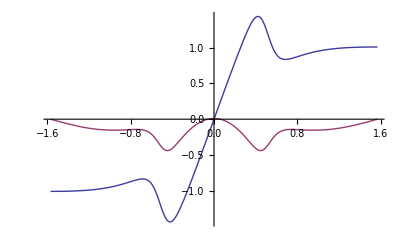

```mathematica
Plot[ {CN,CT} ,{alpha,-Pi/2, Pi/2}]
```

```mathematica
ap
```

0.5

```mathematica
awp
```

0.1

```mathematica
Cm
```

-0.05 (1-1/(1+2.71828^(-20. (-0.5-alpha)))-1/(1+2.71828^(-20. (-0.5+alpha))))-0.1 (1/(1+2.71828^(-20. (-0.5-alpha)))+1/(1+2.71828^(-20. (-0.5+alpha)))) Sign[alpha]

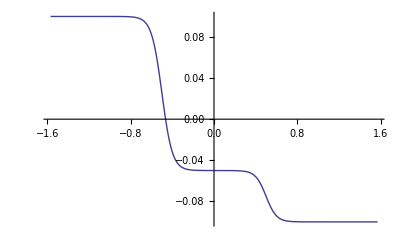

```mathematica
Plot[ {Cm} ,{alpha,-Pi/2, Pi/2}]
```

```mathematica
o
```

o

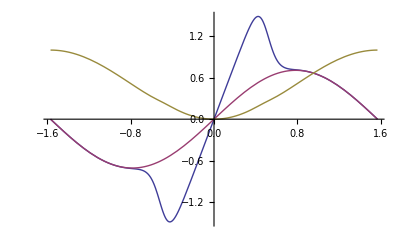

```mathematica
Plot[ {CL,(1/Sqrt[2]) y1,Cdi} ,{alpha,-Pi/2, Pi/2}]
```

```mathematica
DxCL
```

DxCL

```mathematica
CMoment:=(1-1/(1+Power[2.71828,(-2*(-an-alpha))/awn])-1/(1+Power[2.71828,(-2*(-ap+alpha))/awp]))*Cm0+(1/(1+Power[2.71828,(-2.*(-an-alpha))/awn])+1/(1+Power[2.71828,(-2*(-ap+alpha))/awp]))*Cmfs*Sign[alpha];
```